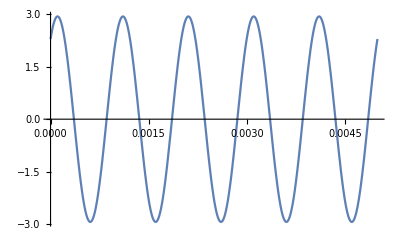

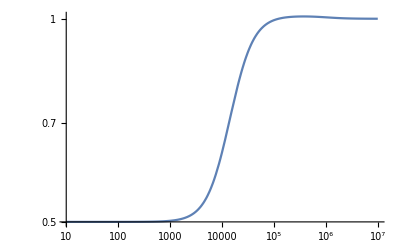

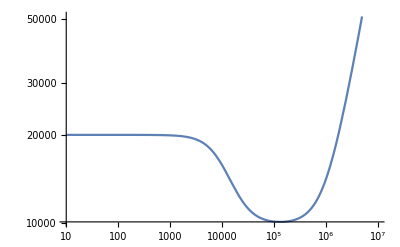

```mathematica
ClearAll["Global`*"];

(* Počítání přenosu a vstupní impedance *)
f = 1000;
U = 4.2 + 3.1ⅉ;
R1 = 10*10^3;
R2 = 10 * 10^3;
L = 10 * 10^-3;
Cc = 10 * 10^-9;

tmax = 0.005;
zc = 1/(ⅉ*ω*Cc);
zl = ⅉ*ω*L;

z2 = R2 + zl;
z1 = (R1 * zc)/(R1 + zc);

Plot[Im[U * z2/(z1 + z2) * Exp[ⅉ*ω*t]] /. {ω ->  2*π*f}, {t, 0, tmax}]
(* obvod si můžeme překreslit jako odporový dělič *)
(* zL = ⅉωL, zC = 1/ⅉωC, z1 = (R1 * zC)/(R1 + zC), z2 = R2 + zL *)

(* Uout = U * z2/(z1 + z2) *)
(* přenos = Uout/U, vstupní impedance = z1 + z2 *)

A = z2/(z1 + z2);
Z = z1 + z2;

LogLogPlot[Abs[A], {ω, 10, 10^7}] (* Použijeme logaritmické měřítko *)
LogLogPlot[Abs[Z], {ω, 10, 10^7}] (* Použijeme logaritmické měřítko *)

(* Černá skříňka = pouze zapíšeme přenos = Uout/U *)
(* Impedance černé skříňky: *)
```